```mathematica
(*Avtomatsko shranjevanje notebook-a*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# 2. domača naloga 2025/26 - 1.del

## 1. naloga

a) Izračunajte neskončno vsoto 1+1/9+1/25+1/49+1/81+...
b) Izračunajte limito funkcije 
		f(x) = (sin(x)-x)/x^3,
    ko gre x proti 0.
c) Izračunajte ploščino lika, ki ga omejujejo graf funkcije g(x) = sin(x)+x^2, abscisna os ter navpičnici x=0 in x=2π.
d) Izračunajte ploščino lika, ki ga omejujeta grafa funkcij g(x) = sin(x)+x^2 in g1(x) = sin(x) + x^5/5.

```mathematica
(*a*) a[x_]=.08(2x+1)^-2;
```

```mathematica
Sum[a[x],{x,0,Infinity}]
```

(.08 π^2)/8

```mathematica
(*b*) f[x_]:= (Sin[x]-x)/x^3;
```

```mathematica
Limit[f[x],x->0]
```

-1/6

```mathematica
(*c*)g = Sin[#]+#^2&;
```

```mathematica
Integrate[g[x],{x,0,2Pi}]
```

(8 π^3)/3

```mathematica
(*d*)g1 = Sin[#]+#^5/5&;
```

```mathematica
Solve[g[x]-g1[x] == 0,x,Reals]
```

{{x→0},{x→0},{x→}}

```mathematica
Plot[{g[x],g1[x]},{x,-1,2}];
```

```mathematica
Integrate[g[x]-g1[x],{x,0,5^(1/3)}]
```

5/6

## 2. naloga

a)  Definirajte funkcijo A(m,n), ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte determinanto, rang in lastne vrednosti matrike . Kaj opazite?
c)  Narišite vektorje, ki ustrezajo stolpcem matrike . S pomočjo ukaza InfinitePlane na sliko narišite še ravnino, v kateri ti trije vektorji ležijo. 
d) Določite parametra, s katerima lahko prvi stolpec matrike A(3,3) izrazimo z drugima dvema.
e) Določite cela števila α, x_1,x_2 in x_3, ki zadoščajo enakosti 
		M (x_1
x_2
x_3) = (-3
-5
-9
-11) ,
    kjer je M matrika, podana kot A(4,3)+αI, kjer I označuje identično matriko ustrezne velikosti. Rešitev zapišite v eni vrstici.

```mathematica
(*a*) A[n_,m_]:=Table[i+j,{i,1,n},{j,1,m}]
```

```mathematica
(*b*)Am = A[3,3]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
Det[Am]
MatrixRank[Am]
Eigenvalues[Am]
```

0

2

{6+√42,6-√42,0}

```mathematica
(*c*)At = Transpose[A];
```

```mathematica
vektorji = ResourceFunction["PlotVector3D"][At];
ravnina = Graphics3D[InfinitePlane[At]];
```

```mathematica
Show[vektorji, ravnina];
```

```mathematica
(*d*) a= At[[1]]; b = At[[2]];c = At[[3]];
```

```mathematica
Solve[x a+y b==c,{x,y}]
```

{{x→-1,y→2}}

```mathematica
(*e*)
Solve[(A[4,3]+x IdentityMatrix[{4,3}]).{x1,x2,x3}=={-3,-5,-9,-11},{x,x1,x2,x3}]
```

```mathematica
{{x->-2,x1->-1,x2->-1,x3->0},{x->-2/11,x1->-22/17,x2->-77/17,x3->55/17}}//TableForm
```

x→-2 | x1→-1 | x2→-1 | x3→0
x→-2/11 | x1→-22/17 | x2→-77/17 | x3→55/17

## 3. naloga

V datoteki ‘vreme.xlsx’ se nahajajo podatki o najvišjih in povprečnih mesečnih temperaturah v Ljubljani v letu 2025. Podatke uvozite v Mathematico.

```mathematica
pot = NotebookDirectory[];
SetDirectory[pot];
podatki = First[Import["vreme.xlsx", "Dataset", HeaderLines-> 1]]
```

a) Grafično predstavite podatke o najvišjih mesečnih temperaturah (graf naj bo čim bolj podoben spodnjemu). Pri tem vrednosti temperatur in številke mesecev z ustreznimi poizvedbami preberite iz uvožene tabele.
b) Napišite poizvedbo, ki bo vrnila imena ‘toplih mesecev’ - to so tisti meseci, katerih povprečna temperatura je višja ob 15 stopinj. Poizvedbo poskusite napisati v eni vrstici.

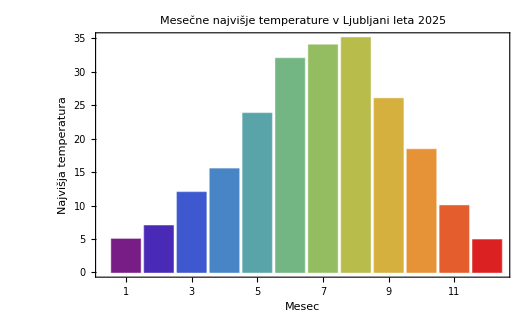

```mathematica
(*a*)
```

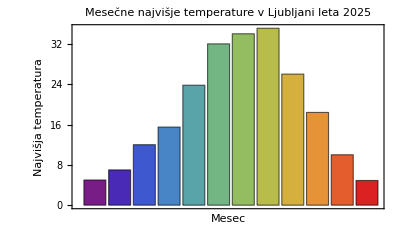

```mathematica
BarChart[podatki[All,"Najvišja"]//Normal,ChartLabels->{podatki[All,"Mesec"]//Normal,None},PlotLabel->"Mesečne najvišje temperature v Ljubljani leta 2025",ChartStyle->"Rainbow", Frame -> True, FrameLabel->{Mesec, Najvišja temperatura }]
```

```mathematica
topli = podatki// Query[Select[#Povprečna >15&]]
```